# Gaussian PDF

by Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]] (* type of gray *)
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255] (* Pastel Green *)
```

```mathematica
(* SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]](* white *)
```

```mathematica
(* SetOptions[EvaluationNotebook[],FontColor->RGBColor[0/255,0/255,0/255]] (* black *)
```

## Initialize Symbols and Notation

## Normal Distribution Function

Definition of the Distribution function:

```mathematica
ClearAll[μ,ρ,σ]
```

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

Exploring influence of μ and σ, we observe:

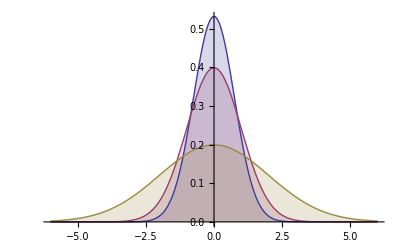

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[μ,σ],x],{μ,{0}},{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

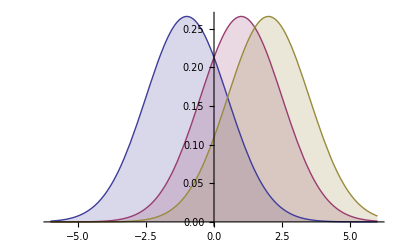

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[μ,σ],x],{μ,{-1,1,2}},{σ,{1.5}}],{x,-6,6},Filling->Axis]
```

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],x]
```

ⅇ^(x μ+(x^2 σ^2)/2)

## BiNormal Distribution Function

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}],{x,y}]
```

(ⅇ^(1/2 (-((x-μ_1) (y ρ σ_1-ρ μ_2 σ_1-x σ_2+μ_1 σ_2))/((-1+ρ^2) σ_1^2 σ_2)-((y-μ_2) (-y σ_1+μ_2 σ_1+x ρ σ_2-ρ μ_1 σ_2))/((-1+ρ^2) σ_1 σ_2^2))))/(2 π √(σ_1^2 σ_2^2-ρ^2 σ_1^2 σ_2^2))

```mathematica
ParallelTable[Plot3D[PDF[MultinormalDistribution[{-1,1},{{1,ρ 2},{ρ 2,4}}],{x,y}],{x,-3,3},{y,-6,6},PlotRange->All,MeshFunctions->{#3&},MeshShading->{None,Red,None,Yellow},PlotPoints->25],{ρ,{-.7,-0.4,0,0.3,0.5,0.8}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
MomentGeneratingFunction[BinormalDistribution[ρ],{x,y}]
```

ⅇ^(x^2/2+y^2/2+x y ρ)